```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

## Import Data

```mathematica
xdata={20,40,60,80,100,120,140,160,180,200};
ydata={33,30,27,26,23,20,19,17,18,12};
```

```mathematica
Length/@{xdata,ydata}
```

{10,10}

```mathematica
dy=Sqrt/@ydata//N
```

{5.74456,5.47723,5.19615,5.09902,4.79583,4.47214,4.3589,4.12311,4.24264,3.4641}

```mathematica
n=Length[xdata]
```

10

## Creating Table

```mathematica
Transpose[{xdata,ydata,Round[dy,0.1]}]//TeXForm//CopyToClipboard
```

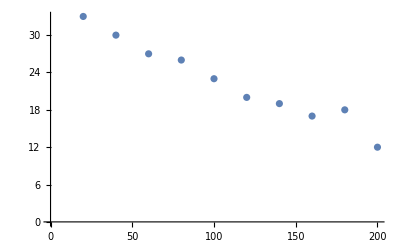

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

```mathematica
logy=Log/@ydata//N
```

{3.49651,3.4012,3.29584,3.2581,3.13549,2.99573,2.94444,2.83321,2.89037,2.48491}

```mathematica
dlogy=Table[dy[[i]]/ydata[[i]],{i,1,Length[ydata]}]
```

{0.174078,0.182574,0.19245,0.196116,0.208514,0.223607,0.229416,0.242536,0.235702,0.288675}

```mathematica
Table[Log[Around[ydata[[i]],dy[[i]]]],{i,1,Length[ydata]}]
```

{3.500.17,3.400.18,3.300.19,3.260.20,3.140.21,3.000.22,2.940.23,2.830.24,2.890.24,2.480.29}

```mathematica
Transpose[{xdata,Round[logy,0.01],Round[dlogy,0.01]}]//TeXForm//CopyToClipboard
```

## Unweighted Linear Regression

```mathematica
sumxv1=Total[xdata]
sumyv1=Total[logy]
sumx2v1=Total[#^2&/@xdata]
sumxyv1=Sum[xdata[[i]]logy[[i]],{i,1,Length[xdata]}]
```

1100

30.7358

154000

3220.2

```mathematica
Δv1=n(sumx2v1)-(sumxv1)^2
```

330000

```mathematica
(sumx2v1 sumyv1-sumxv1 sumxyv1)/Δv1
```

3.60938

```mathematica
1/Δv1 (n sumxyv1 - sumxv1 sumyv1)
```

-0.00487092

```mathematica
LinearModelFit[Transpose[{xdata,logy}],x,x]
```

FittedModel[3.60938-0.00487092 x]